# CO2 Phase Diagram

## PC-SAFT (Perturbed-Chain Statistical Associating Fluid Theory)

Andy Ylitalo, with guidance from Dr. Huikuan Chao and mentorship from Prof. Zhen-Gang Wang

## Questions

## 0. Setup

```mathematica
SetDirectory[FileNameJoin[{"C:","Users","Andy.DESKTOP-CFRG05F","OneDrive - California Institute of Technology", "Documents", "Research", "Wang", "PC-SAFT"}]];
```

## 1. Equations

```mathematica
d[σ_,β_,ϵ_]:=σ(1-0.12Exp[-3ϵ β]);  (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
```

### Free energy of ideal gas

```mathematica
βfIG[ρ_,N_:2]:= ρ/N(Log[ρ /N ]-1);
```

Cubed expression is the thermal de Broglie wavelength, λT = h / Sqrt[2 π m k T]. m is the mass of a single particle (in this case, CO2 atom, kg). Note that ρ is divided by N to get the density of molecules, not segments.
7.31*^-26 kg is the mass of a carbon dioxide atom (44.01 amu).

### Free energy of hard-sphere liquid

Note that ξ[ρ,σ,3] represents the total packing fraction and is therefore dimensionless. In general, ξ[ρ,σ,n] has dimensions of (length)^(n-3).

```mathematica
ξ[ρ_,d_,j_]:=π/6 ρ d^j;
```

```mathematica
βfHS[ρ_,d_]:=6/π( (3 ξ[ρ,d,1]ξ[ρ,d,2])/(1-ξ[ρ,d,3])
+ (ξ[ρ,d,2])^3/(ξ[ρ,d,3](1-ξ[ρ,d,3])^2)
+ ((ξ[ρ,d,2])^3/(ξ[ρ,d,3])^2-ξ[ρ,d,0])Log[1-ξ[ρ,d,3]] );
```

### Free energy of association

```mathematica
gii[ρ_,d_]:=1/(1-ξ[ρ,d,3])+ 3ξ[ρ,d,2] d/ (2(1-ξ[ρ,d,3])^2)+ (ξ[ρ,d,2])^2d^2 / (2(1-ξ[ρ,d,3])^3); (* radial pair distribution function for segments of component i in the hard-sphere system *)
```

```mathematica
βfAssoc[ρ_,d_,N_:2]:=-(N-1)/N ρ Log[gii[ρ,d]];
```

### Free energy of dispersion

First, load the constants for the polynomial approximation of the integrals I1 and I2 in Gross and Sadowski (2001). We refer to them here as J1 and J2 according to the nomenclature used by Xu et al. (2012).

```mathematica
JConstants=Import[FileNameJoin[{"Data","J_integral_const_a_b.csv"}]];
```

```mathematica
a0=JConstants[[2;;-1, 2]];
a1 = JConstants[[2;;-1, 3]];
a2 = JConstants[[2;;-1, 4]];
b0 = JConstants[[2;;-1, 5]];
b1 = JConstants[[2;;-1, 6]];
b2 = JConstants[[2;;-1, 7]];
```

```mathematica
a= a0 +  a1/2 ; (* full formula: a = a0 + (N-1)/N a1 + (N-1)/N (N-2)/N a2 *)
b= b0 +  b1/2 ; (* full formula: b = b0 + (N-1)/N b1 + (N-1)/N (N-2)/N b2 *)
```

```mathematica
J1[ρ_,d_,N_]:=Sum[a[[i]](ξ[ρ,d,3])^(i-1),{i,1,Length[a]}]
J2[ρ_,d_,N_]:=Sum[b[[i]](ξ[ρ,d,3])^(i-1),{i,1,Length[a]}]
```

```mathematica
M[ρ_,d_,N_:2]:=1+N(8 ξ[ρ,d,3] - 2 (ξ[ρ,d,3])^2)/(1-ξ[ρ,d,3])^4+ (1-N)(20 ξ[ρ,d,3] - 27(ξ[ρ,d,3])^2 + 12 (ξ[ρ,d,3])^3 - 2(ξ[ρ,d,3])^4)/((1-ξ[ρ,d,3])^2(2-ξ[ρ,d,3])^2); (* dimensionless--might be a typo (compare eqn 25 of Gross and Sadowski and the eqn for M below eqn 6 in Xu et al *)
```

```mathematica
βfDisp[ρ_,σ_,β_,ϵ_,N_:2]:=-π ρ^2 (2 J1[ρ,d[σ,β,ϵ],N] β ϵ + N /M[ρ,d[σ,β,ϵ],N] J2[ρ,d[σ,β,ϵ],N] (β ϵ)^2) σ^3;
```

### Total Free Energy

```mathematica
βf[ρ_,σ_,β_,ϵ_,N_:2]:=βfIG[ρ]+βfHS[ρ,d[σ,β,ϵ]]+βfAssoc[ρ,d[σ,β,ϵ],N]+βfDisp[ρ,σ,β,ϵ,N];
```

### Chemical potential

```mathematica
βμ[ρ_,σ_,β_,ϵ_,N_:2]:=D[βf[ρprime,σ,β,ϵ,N],ρprime]/.ρprime->ρ;
```

### Pressure

```mathematica
βp[ρ_,σ_,β_,ϵ_]:= -βf[ρ,σ,β,ϵ]+ρ βμ[ρ,σ,β,ϵ];
```

## 2. Plot

```mathematica
kB= 1.38065*^-23;  (* Boltzmann constant [J/K] *)
T=290; (* temperature [K] *)
ϵCO2=170.5 ; (* attractive well depth, from Xu et al. 2012 JCP [J] *)
σCO2= 2.79*^-10; (* bead size [m] *)
σCO2Ref = 1; (* use bead size as reference length for system *)
dCO2 = σCO2*(1-0.12*Exp[-3ϵCO2*βParam]); (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
ρmin=0; (* minimum mass density to plot[kg/m^3] *)
ρmax = 1100; (* maximum mass density to plot [kg/m^3] *)
NCO2 = 2; (* number of beads for one carbon dioxide molecule [nondim] *)
MBeadCO2= 0.044/NCO2; (* molar mass of one bead of carbon dioxide [kg/mol] *)
NA = 6.022*^23; (* Avogadro's number [molecules/mol] *)
ρCO2Conv=σCO2^3*NA/MBeadCO2; (* convert kg/m^3 -> molecules/kg *)
Pa2MPa = 1*^-6; (* multiplicative conversion from Pa -> MPa *)
pCO2Conv = Pa2MPa*kB *T*σCO2^(-3);
```

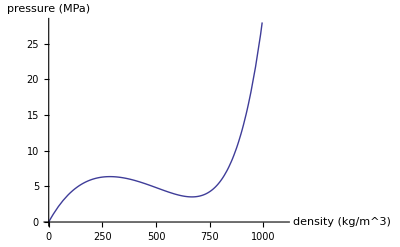

```mathematica
Plot[βp[ρ*ρCO2Conv,σCO2Ref,1/T,ϵCO2]*pCO2Conv,{ρ,ρmin, ρmax},AxesLabel->{"density (kg/m^3)","pressure (MPa)"}]
```

## 2. Numerical Solving

### Critical Point

Occurs where both first and second derivatives of pressure with respect to density are 0.

```mathematica
ρCActual = 413.45063; (* kg/m^3 *)
TCActual = 304.25; (* K *)
```

```mathematica
criticalPoint =FindRoot[{D[D[βp[ρC*ρCO2Conv,σCO2Ref,1/TC,ϵCO2],ρC],ρC]==0,D[D[D[βp[ρC*ρCO2Conv,σCO2Ref,1/TC,ϵCO2],ρC],ρC],ρC]==0},{{ρC,ρCActual},{TC,TCActual}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ρC→420.354,TC→301.963}

The critical point is within 2% of the actual value. Below, the critical pressure is calculated in MPa. The actual value is 7.39 MPa (this time, within 4%)

```mathematica
pC =βp[ρC*ρCO2Conv,σCO2Ref,1/TC,ϵCO2]*pCO2Conv/.criticalPoint
```

7.15849

## 3. Fit Parameters from Data

Rather than using the parameters given to me by Xiaofei’s paper (Xu et al., 2012), I want to estimate the parameters (N, σ, ϵ) for CO2 using Mathematica’s FindFit function. We’ll start by assuming N = 2.

```mathematica
co2EOSData = Cases[Import [FileNameJoin[{"Data","co2_eos_data.csv"}]],{_?NumberQ,___}];(* in the format ρ [kg/m^3], T [K], p [MPa]; "Cases" command with options "_?NumberQ,___" skips rows that don't start with a number   *)
```

```mathematica
Clear[T]
```

```mathematica
FindFit[co2EOSData,βp[ρ*σ^3*(NA*1*^-30)/MBeadCO2,1,1/T,ϵ]*Pa2MPa*kB *1*^30*T*σ^(-3),{{σ,2.79},{ϵ,170}},{ρ,T}] (* σ in Angstroms, ϵ in kB *)
```

{σ→2.79682,ϵ→171.406}